## Defined Functions

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Quiet[ResourceFunction["PolygonMarker"]];
Get["CustomTicks.m"]

ScienForm::usage="Turn number into scientific form.";
ScienForm[num_]:=ScientificForm[num+0.,NumberFormat->(If[ToExpression[#1]==1,Superscript[10,#3],Automatic]&)]

ConvertHelper[xdata_,xrange_,Mag_]:=Module[{xdataN,xrangeN,tickFunc,ticks},
xrangeN=If[AllTrue[xrange,NumberQ],xrange,{Min[xdata],Max[xdata]}];
{xdataN,xrangeN,tickFunc}=If[NumberQ[Mag],
{xdata*Mag,xrangeN*Mag,LinTicks},
{Log10[xdata],Log10[xrangeN],LogTicks}];
ticks=tickFunc[xrangeN[[1]],xrangeN[[2]],ShowMinorTicks->False,MajorTickLength->0.03];
{xdataN,xrangeN,ticks}
]

ConvertDataWTicks[data_,range_,Mag_,ticks_:None]:=Module[{dataN,x,y,xrangeN,yrangeN,xticks,yticks},
If[ticks=!=None,Return[{data,range,ticks}]];
dataN=If[Length@Dimensions[data]==2,{data},data];
{x,y}={dataN[[;;,;;,1]],dataN[[;;,;;,2]]};
{{x,xrangeN,xticks},{y,yrangeN,yticks}}=ConvertHelper@@@Transpose[{{x,y},range,Mag}];
dataN=Transpose[Transpose[{x,y},1<->2],2<->3];
{dataN,{xrangeN,yrangeN},{{yticks,None},{xticks,None}}}
]

LegendStyle::usage="Generate line legend.
Params: legend, colorlist, vertical spacing, layout format";
LegendStyle[legend_,colorlist_,space_:-2,layout_:Automatic]:=
LineLegend[Directive[colorlist[[#]],Thickness[0.01]]&/@Range[Length[#]],#,LabelStyle->{15},LegendMarkers->MarkerZoom[10],LegendLayout->layout,LegendMarkerSize->{60,50},Spacings->{0.3,space}]&@legend

LegendDashStyle::usage="Generate dashed line legend.
Params: legend, color,";
LegendDashStyle[legend_,color_]:=
LineLegend[{Directive[color,Thickness[0.01]],Directive[color,Dashing[0.02],Thickness[0.008]]},legend,LabelStyle->{15},LegendMarkerSize->{{65,45},{40,45}},LegendMarkers->{MarkerZoom[10][[1]],""},Spacings->{0.3,-2}]

StyleGenerator::usage="Generate directive plotstyle with color list.
Params: colorlist, data";
StyleGenerator[colorlist_,data_]:=Module[{len,colorlistN},
colorlistN=If[Head[colorlist]===List,colorlist,{colorlist}];
len=If[Length@Dimensions[data]==2,1,Dimensions[data][[1]]];
Table[{colorlistN[[i]],Thickness[0.012]},{i,1,len}]
]

MarkerZoom::usage="Generate marker style. (Mathematica has a problem in outputting the plotmarkers.)
Params: magnitude";
MarkerZoom[mag_]:=Module[{fm2,fm},
fm[name_String,size_:mag]:=ResourceFunction["PolygonMarker"][name,Offset[size],EdgeForm[]];
fm2[name_String,size_:mag]:=ResourceFunction["PolygonMarker"][name,Offset@size,{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[1]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],0.75]}];fm2/@{"Circle","Square","Diamond","UpTriangle","DownTriangle"}
]

LocalGlobalPlot[data_,colorlist_,dataWM_,colorWM_,range_,labels_,legendPos_,Mag_,exportName_:"",legendWMPos_:""]:=Module[{dataN,rangeN,ticksN,localPlot,globalPlot,finalPlot,dataWMN,wmPlot,plotMethod,plotdata,legends,legendsPos},
{dataN,rangeN,ticksN}=ConvertDataWTicks[data,range,Mag];
localPlot=ListPlot[dataN[[;;-2]],Joined->True,PlotRange->All,PlotStyle->Thread@{Opacity[0.5],Dashing[0.02],Thickness[0.01],ColorData[2,#]&/@Range[100]}];
globalPlot=GlobalPlot[dataN[[-1]],colorlist,rangeN,labels,Mag,"",ticksN];

If[dataWM=!="",dataWMN=ConvertDataWTicks[dataWM,range,Mag][[1]];
wmPlot=ListPlot[dataWMN,Joined->True,PlotMarkers->MarkerZoom[9],PlotStyle->Directive[colorWM,Thickness[0.01]]];
plotdata={globalPlot,localPlot,wmPlot},plotdata={globalPlot,localPlot}];
finalPlot=Legended[Show[plotdata,FrameLabel->labels],
Placed[LegendDashStyle[{"Global", "Local"},colorlist],legendPos]];
finalPlot=If[legendWMPos=!="",Legended[finalPlot,
Placed[LegendDashStyle[{"Well-Mixed"},ColorData[97,5]],legendWMPos]], finalPlot];
If[exportName=!="",Export["Plot/"<>exportName<>".pdf",finalPlot]];
finalPlot]


GlobalPlot::usage="Plot data with global data. Plot global with colorGlob.
Params: data, colorlist, range, labels, xMagDec,yMagDec, exportName";
GlobalPlot[data_,colorlist_,range_,labels_,Mag_,exportName_:"",ticks_:None,markers_:MarkerZoom[10]]:=Module[{globalPlot,finalPlot,dataN,rangeN,ticksN},
{dataN,rangeN,ticksN}=ConvertDataWTicks[data,range,Mag,ticks];
ListPlot[dataN,Joined->True,Frame->True,PlotRange->rangeN,FrameTicks->ticksN];
globalPlot=ListPlot[dataN,Joined->True,PlotMarkers->markers,Frame->True,Axes->False,FrameLabel->labels,FrameStyle->Directive[Black,Thickness[0.006],FontSize->18],FrameTicks->ticksN,PlotRange->rangeN,PlotStyle->StyleGenerator[colorlist,data]];
globalPlot=If[NumberQ[Mag[[2]]]&&Mag[[2]]>1,Show[globalPlot,Epilog->Inset[Style[Row[{"x",ScienForm[1./Mag[[2]]]}],18],Offset[{-5,-8},Scaled[{0.1,1.1}]]],ImagePadding->{{All,All},{All,25}},PlotRangeClipping->False],globalPlot];
If[exportName=!="",Export["Plot/"<>exportName<>".pdf",globalPlot]];
globalPlot
]

FitFreqPre::usage="Prepare the FitFreq data into max fitness and frequencies.
Params: fitdata, dN";
FitFreqPre[fitdata_,dN_,tnew_]:=Module[{fitSplit,fitSplitC,meandata,mft,maxfit,maxfitFreq},
fitSplit=SequenceSplit[#,{";"}]&/@fitdata;
fitSplitC=Prepend[#,Table[{0,0},dN+1]]&/@Map[SequenceSplit[#,{","}]&,fitSplit[[;;,;;,2;;]],{2}];
meandata=Transpose@Mean@Partition[#,ngap+1,ngap]&@Mean@fitSplitC;
maxfit=Transpose[{tnew,#}]&/@(Drop[#,{2}]&/@meandata[[;;,;;,1]]);
maxfitFreq=Transpose[{tnew,#}]&/@(Drop[#,{2}]&/@meandata[[;;,;;,2]]);
maxfit[[All,All,2]]-=Mean@maxfit[[;;-2,1,2]];
{maxfit,maxfitFreq}
]

Importtfit::usage="Prepare the tfit data.
Params: filename";
Importtfit[filename_]:=Partition[#,2]&/@Import[filename<>".tfit","Table"]

AllDataPre::usage="Prepare all the data.
Params: filename";
AllDataPre[filename_,std_:False]:=Module[{datafit,datahet,datatfit,datarel,maxfit,maxfitFreq,meanHetC,het,datarelC,meanRel,rel,dN},
dN=ToExpression@StringSplit[filename,{"D","/","N"}][[-2]];
datafit=Import[filename<>".fit","Table"];
{maxfit,maxfitFreq}=FitFreqPre[datafit,dN,tnew];
datahet=SequenceSplit[#,{","}]&/@Import[filename<>".het","Table"];
datatfit=Importtfit[filename];
datarel=SequenceSplit[#,{","}]&/@Import[filename<>".rel","Table"];
datarelC=Prepend[#,1000]&/@datarel[[;;,;;,2]];
If[std,
(*With std*)
meanHetC=(#-Mean[#[[1]]])&/@(Drop[#,{2}]&/@Partition[#,ngap+1,ngap]&@Transpose@(Prepend[#,0]&/@datahet[[All,All,-1]]));
het={Transpose[{tnew,#}]&@((MeanAround/@Transpose@Flatten[Transpose[meanHetC,2<->3],1]))};
meanRel=1000-Mean@Partition[#,ngap+1,ngap]&@(MeanAround/@Transpose[datarelC]),
(*with only mean*)
meanHetC=Mean@Partition[#,ngap+1,ngap]&/@Transpose@Mean@(Prepend[#,Table[0,dN+1]]&/@datahet[[All,All,2;;]])/2;
het=Transpose[{tnew,#}]&/@(Drop[#,{2}]&/@meanHetC);
meanRel=1000-Mean@Partition[#,ngap+1,ngap]&@Mean@datarelC
];
rel=Transpose[{tnew,#}]&@Drop[#,{2}]&@meanRel;
If[dN==1,{maxfit[[1]],maxfitFreq[[1]],datatfit,het[[1]],rel},{maxfit,maxfitFreq,datatfit,het,rel}]
]

MeanMaxTraj::usage="Prepare trajectories of maximun fitness and mean fitness.
Params: filename";
MeanMaxTraj[filename_]:=Module[{dN,tlist,tfitTraj,datafit,fitSplit,globalTraj,localTraj},
dN=ToExpression@StringSplit[filename,{"D","/","N"}][[-2]];
tfitTraj=Mean[Partition[#,2]&/@Import[filename<>".tfit","Table"]];
tlist=tfitTraj[[;;,1]];
datafit=SequenceSplit[#,{";"}]&/@Import[filename<>".fit","Table"];
fitSplit=Prepend[#,Table[{0,0},dN+1]]&/@Map[SequenceSplit[#,{","}]&,datafit[[;;,;;,2;;]],{2}];
globalTraj=Transpose[{tlist,Mean@fitSplit[[;;,2;;,-1,1]]}];
localTraj=Transpose[{tlist,Mean@Mean@Transpose[fitSplit[[;;,2;;,;;-2,1]],2<->3]}];
{tfitTraj,localTraj,globalTraj}
]

SpeedHA::usage="Calculate adaptation speed by linearly fit the latter half.
Params: tfit, Population size";
SpeedHA[tfitdata_,PopNum_,std_:False]:=Module[{sp,spms},
sp=Map[Last@Fit[#[[Round[Length@#/2];;]], {1,x},x]/.x->1&,tfitdata,{2}];
spms=If[std,MeanAround/@sp,Mean/@sp];
Transpose[{ToExpression/@PopNum,spms}]
]

RatioW::usage="Calculate ratio of the adaptation speed. Compared with a well-mixed population.
Params: tfitdata, speed from well-mixed, Population size ";
RatioW[tfitdata_,wmHA_,PopNum_,std_:False]:=Module[{speed,spms,ratios},
speed=SpeedHA[tfitdata,PopNum,std];
ratios=speed[[;;,2]]/wmHA[[;;,2]];
{speed,Transpose[{ToExpression/@PopNum,ratios}]}
]
```

## Import Data

```mathematica
tgap=100;ngap=tgap/10+1;type="M5E-4R1.25E-3";defaultType="100D100N10000M5E-4R1.25E-3";
tnew={0,10,20,30,40,50,60,70,80,90,100};
deme1="100D1N";deme10="100D10N";deme100="100D100N";
PN={"10","100","1000","10000","100000","1000000"};

nameSS="SS";nameSB="SB";nameBB="BB";nameBS="BS";nameSSIS="SSIS";nameBBIS="BBIS";
pathSS="DStSt/";pathSB="DStBu/";pathBS="DBuSt/";pathBB="DBuBu/";
pathSSIS=pathSS<>"IndSync/";pathBBIS=pathBB<>"IndSync/";pathWMC="DWellMix/C/";pathWMB="DWellMix/B/";
nameSSWM="SS&WM";nameSBWM="SB&WM";nameBBWM="BB&WM";nameBSWM="BS&WM";
nameWMC="WMC";nameWMB="WMB";nameBBISWM="BBIS&WM";nameSSISWM="SSIS&WM";

outputStd=True;
fileWMC=pathWMC<>"100D1N1000000M5E-4R1.25E-3";colorWMC=ColorData[97,5];
{maxfitWMC,maxfitFreqWMC,datatfitWMC,hetWMC,relWMC}=AllDataPre[fileWMC,outputStd];
fileWMB=pathWMB<>"100D1N1000000M5E-4R1.25E-3";colorWMB=ColorData[97,9];
{maxfitWMB,maxfitFreqWMB,datatfitWMB,hetWMB,relWMB}=AllDataPre[fileWMB,outputStd];
fileSS=pathSS<>defaultType;colorSS=ColorData[97,2];
{maxfitSS,maxfitFreqSS,datatfitSS,hetSS,relSS}=AllDataPre[fileSS,outputStd];
fileSB=pathSB<>defaultType;colorSB=ColorData[97,3];
{maxfitSB,maxfitFreqSB,datatfitSB,hetSB,relSB}=AllDataPre[fileSB,outputStd];
fileBS=pathBS<>defaultType;colorBS=ColorData[97,4];
{maxfitBS,maxfitFreqBS,datatfitBS,hetBS,relBS}=AllDataPre[fileBS,outputStd];
fileBB=pathBB<>defaultType;colorBB=ColorData[97,1];
{maxfitBB,maxfitFreqBB,datatfitBB,hetBB,relBB}=AllDataPre[fileBB,outputStd];
fileSSIS=pathSSIS<>defaultType;colorSSIS=ColorData[97,8];
{maxfitSSIS,maxfitFreqSSIS,datatfitSSIS,hetSSIS,relSSIS}=AllDataPre[fileSSIS,outputStd];
fileBBIS=pathBBIS<>defaultType;colorBBIS=ColorData[97,7];
{maxfitBBIS,maxfitFreqBBIS,datatfitBBIS,hetBBIS,relBBIS}=AllDataPre[fileBBIS,outputStd];

SpeedWMB=SpeedHA[#,PN[[3;;]],outputStd]&@(Importtfit[pathWMB<>deme1<>#<>type]&/@PN[[3;;]]);
SpeedWMC=SpeedHA[#,PN[[3;;]],outputStd]&@(Importtfit[pathWMC<>deme1<>#<>type]&/@PN[[3;;]]);
{SpeedSS10,ratioSS10}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSS<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedSS100,ratioSS100}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSS<>deme100<>#<>type]&/@PN[[1;;-3]]);
{SpeedSB10,ratioSB10}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSB<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedSB100,ratioSB100}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSB<>deme100<>#<>type]&/@PN[[1;;-3]]);
{SpeedBS10,ratioBS10}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBS<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedBS100,ratioBS100}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBS<>deme100<>#<>type]&/@PN[[1;;-3]]);
{SpeedBB10,ratioBB10}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBB<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedBB100,ratioBB100}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBB<>deme100<>#<>type]&/@PN[[1;;-3]]);
{SpeedSSIS10,ratioSSIS10}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSSIS<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedSSIS100,ratioSSIS100}=RatioW[#,SpeedWMC, PN[[3;;]],outputStd]&@(Importtfit[pathSSIS<>deme100<>#<>type]&/@PN[[1;;-3]]);
{SpeedBBIS10,ratioBBIS10}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBBIS<>deme10<>#<>type]&/@PN[[2;;-2]]);
{SpeedBBIS100,ratioBBIS100}=RatioW[#,SpeedWMB, PN[[3;;]],outputStd]&@(Importtfit[pathBBIS<>deme100<>#<>type]&/@PN[[1;;-3]]);

SpeedWMCR0=SpeedHA[#,PN[[3;;]],outputStd]&@(Importtfit[pathWMC<>deme1<>#<>"M5E-4R0"]&/@PN[[3;;]]);
{SpeedSSR010,ratioSSR010}=RatioW[#,SpeedWMCR0, PN[[3;;]],outputStd]&@(Importtfit[pathSS<>deme10<>#<>"M5E-4R0"]&/@PN[[2;;-2]]);
{SpeedSSR0100,ratioSSR0100}=RatioW[#,SpeedWMCR0, PN[[3;;]],outputStd]&@(Importtfit[pathSS<>deme100<>#<>"M5E-4R0"]&/@PN[[1;;-3]]);
colorWMCR0=ColorData[97,5];colorSSR0=ColorData[82,1];
```

## Adaption Speed

### Ratios

#### Populationally synced

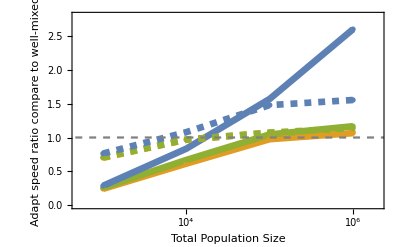

```mathematica
ratio10={ratioSS10,ratioSB10,ratioBB10};ratio100={ratioSS100,ratioSB100,ratioBB100};
colorList={colorSS,colorSB,colorBB};colorListDashed={#,Dashed}&/@colorList;

{plot100,plot10}=GlobalPlot[#1,#2,{{500,2000000},{0,2.8}},{"Total Population Size",Column[{"Adapt speed ratio","compare to well-mixed"},Left,0]},{"log",1}]&@@@{{ratio100,colorList},{ratio10,colorListDashed}};
(*plot100=Legended[plot100,
Placed[LegendStyle[{"Unsynced","Synced dispersal",Column[{"Pop synced sex", "& dispersal"}, Left, -0.1]},colorList,-1.7],{0.34,0.75}]];*)
dashLinePlot=Plot[1,{x,2,7},PlotStyle->{Gray,Dashed}];
Show[plot100,plot10,dashLinePlot]
Export["Plot/Ratio_PS.pdf",%];
LegendStyle[{"Unsynced","Synced dispersal","Pop synced sex & dispersal"},colorList,0,{"Row",1}]
Export["Plot/Ratio_PS_legend.pdf",%];
```

#### Individually synced

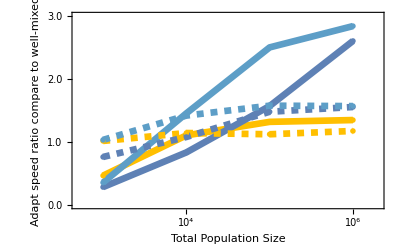

```mathematica
ratio10={ratioSSIS10,ratioBB10,ratioBBIS10};ratio100={ratioSSIS100,ratioBB100,ratioBBIS100};
colorList={colorSSIS,colorBB,colorBBIS};colorListDashed={#,Dashed}&/@colorList;

{plot100,plot10}=GlobalPlot[#1,#2,{{500,2000000},{0,3}},{"Total Population Size",Column[{"Adapt speed ratio","compare to well-mixed"},Left,0]},{"log",1}]&@@@{{ratio100,colorList},{ratio10,colorListDashed}};
plot100=Legended[plot100,
Placed[LegendStyle[{"Indiv synced only","Pop synced only","Both"},colorList,-2.3],{0.3,0.835}]];
dashLinePlot=Plot[1,{x,6.5,15},PlotStyle->{Gray,Dashed}];
Show[plot100,plot10,dashLinePlot]
Export["Plot/Ratio_IS.pdf",%];
```

### Ratio for single structure population

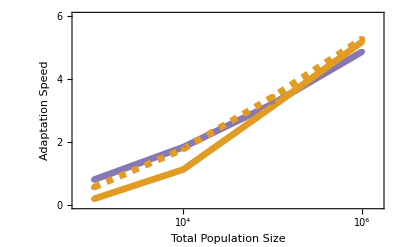

```mathematica
pop={"SS","SB","BS","BB","BBIS","SSIS","SSR0"}[[1]];
nameWM=If[Characters[pop][[1]]=="S","WMC","WMB"];nameWM=If[Characters[pop][[-1]]=="0",nameWM<>"R0",nameWM];
meanSpeed=ToExpression["Speed"<>#]&/@{nameWM,pop<>"100",pop<>"10"};
maxs=Max@meanSpeed[[;;,;;,2]];
ratios=ToExpression["ratio"<>pop<>"100"];
colorList=ToExpression["color"<>#]&/@{nameWM,pop,pop};colorList[[3]]={colorList[[3]],Dashed};

yticks={{0,0,{0.05,0}},{1,1,{1,0},Dashed},{2,2,{0.05,0}},{3,3,{0.05,0}}};
xyticksR={{None,yticks},{{#,,{0.05,0}}&/@ToExpression[PN[[3;;]]],None}};
ratioplot=ListLogLinearPlot[Transpose[{ratios[[All,1]],ratios[[All,2]]}],Joined->True,PlotStyle->{colorList[[2]],Thickness[0.028]},PlotRange->{{1/2.3*10^3,3.2*10^6},{0,2}},PlotRange->{{500,2000000},{-0.0015,Automatic}},Axes->False,PlotMarkers->MarkerZoom[7][[2]],Frame->True,FrameTicks->xyticksR,FrameLabel->{None,"Ratio"},FrameStyle->Directive[Black,Thickness[0.015],FontSize->18],ImageSize->150];

GlobalPlot[meanSpeed,colorList,{{1/1.5*10^3,1.5*10^6},{0,6*10^-3}},{"Total Population Size","Adaptation Speed"},{"log",1000}];
Show[%,Epilog->Inset[ratioplot,{3.8,maxs*1000/1.25}]]
Export["Plot/Speed_"<>pop<>".pdf",%];
```

```mathematica
{5.2,maxs*1000/3.3}
```

### Speed of WM (w/ and w/o sex)

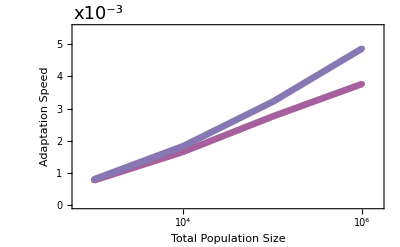

```mathematica
meanSpeed={SpeedWMB,SpeedWMC};
colorList={colorWMB,colorWMC};

Legended[GlobalPlot[meanSpeed,colorList,{{1/1.5*10^3,1.5*10^6},{0,5.5*10^-3}},{"Total Population Size","Adaptation Speed"},{"log",1000}],Placed[LegendStyle[{"Synced sex","Unsynced sex"},colorList],{0.3,0.8}]]
Export["Plot/Speed_WM.pdf",%];
```

### Speed of IS

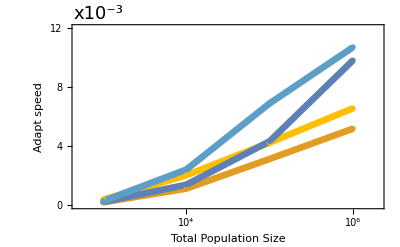

```mathematica
speed100={SpeedSS100,SpeedSSIS100,SpeedBB100,SpeedBBIS100};
colorList={colorSS,colorSSIS,colorBB,colorBBIS};

plot100=GlobalPlot[speed100,colorList,{{500,2000000},{0,0.012}},{"Total Population Size","Adapt speed"},{"log",1000}];Legended[plot100,
Placed[LegendStyle[{"Unsyced","Indiv synced only","Pop synced only","Indiv&pop synced"},colorList],{0.3,0.75}]]
Export["Plot/Speed_IS.pdf",%];
```

## Statistic

### Well-mixed (Const Rec)

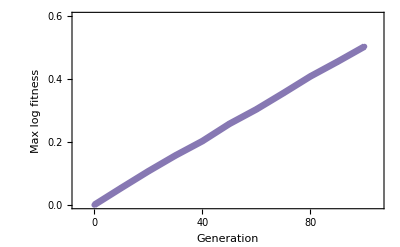

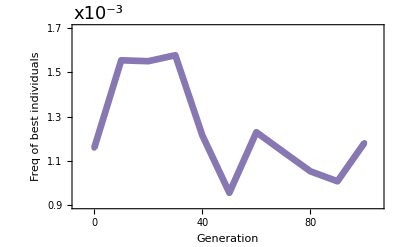

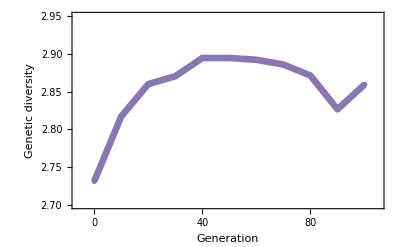

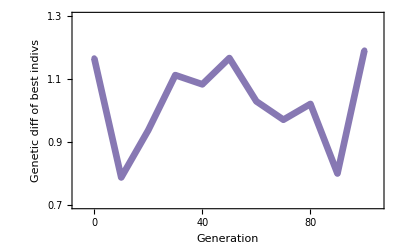

```mathematica
GlobalPlot[maxfitWMC,colorWMC,{{-6,105},{0,0.6}},{"Generation","Max log fitness"},{1,1},"max_fit_"<>nameWMC]
GlobalPlot[maxfitFreqWMC,colorWMC,{{-6,105},{9*10^-4,1.7*10^-3}},{"Generation","Freq of best individuals"},{1,1000},"max_fit_freq_"<>nameWMC]
GlobalPlot[hetWMC,colorWMC,{{-6,105},{2.7,2.95}},{"Generation","Genetic diversity"},{1,1},"het_"<>nameWMC]
GlobalPlot[relWMC,colorWMC,{{-6,105},{0.7,1.3}},{"Generation",Column[{"Genetic diff","of best indivs"},Left,0]},{1,1},"rel_"<>nameWMC]
```

#### Supplement

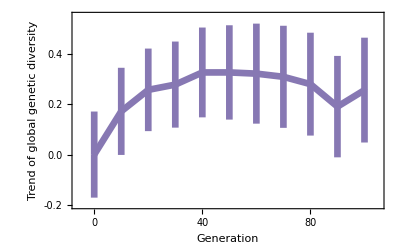

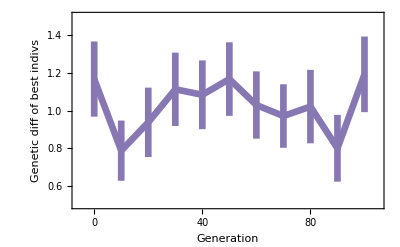

```mathematica
GlobalPlot[hetWMC,colorWMC,{{-6,105},{-0.2,0.55}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_"<>nameWMC<>"_sd"]
GlobalPlot[relWMC,colorWMC,{{-6,105},{0.5,1.5}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_"<>nameWMC<>"_sd"]
```

### Well-mixed (Bursty Rec)

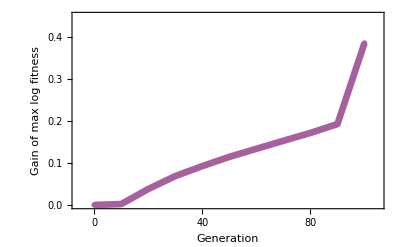

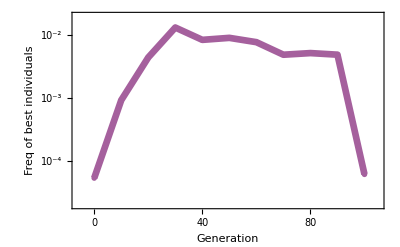

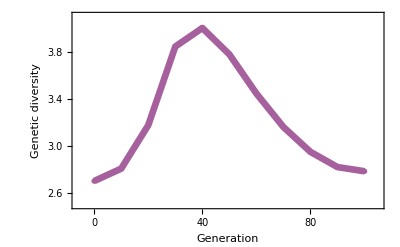

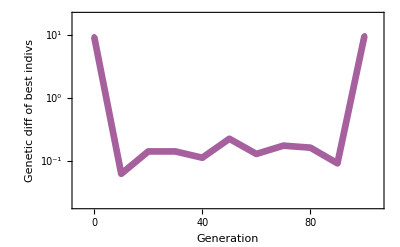

```mathematica
GlobalPlot[maxfitWMB,colorWMB,{{-6,105},{0,0.45}},{"Generation","Gain of max log fitness"},{1,1},"max_fit_"<>nameWMB]
GlobalPlot[maxfitFreqWMB,colorWMB,{{-6,105},{2*10^-5,2*10^-2}},{"Generation","Freq of best individuals"},{1,"log"},"max_fit_freq_"<>nameWMB]
GlobalPlot[hetWMB,colorWMB,{{-6,105},{2.5,4.1}},{"Generation","Genetic diversity"},{1,1},"het_"<>nameWMB]
GlobalPlot[relWMB,colorWMB,{{-6,105},{2*10^-2,2*10}},{"Generation",Column[{"Genetic diff","of best indivs"},Left,0]},{1,"log"},"rel_"<>nameWMB]
```

#### Supplement

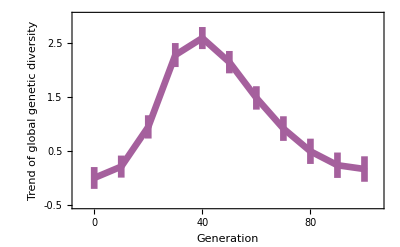

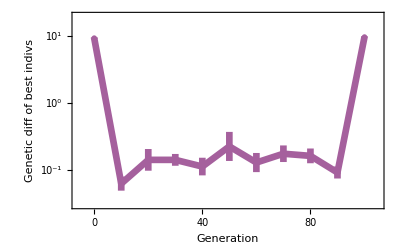

```mathematica
GlobalPlot[hetWMB,colorWMB,{{-6,105},{-0.5,3.0}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_"<>nameWMB<>"_sd"]
GlobalPlot[relWMB,colorWMB,{{-6,105},{0.03,2*10}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameWMB<>"_sd"]
```

### SS

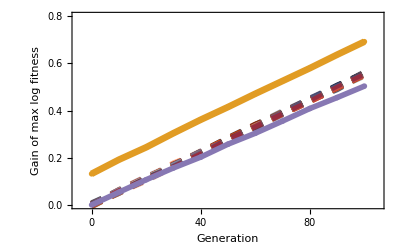

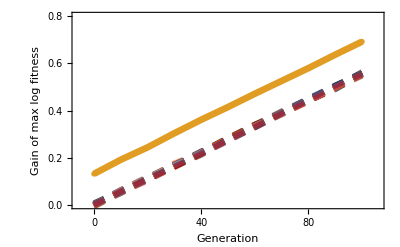

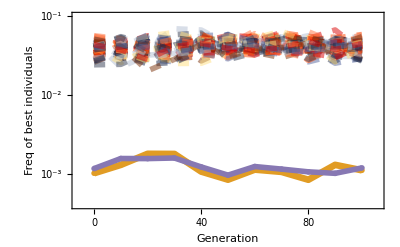

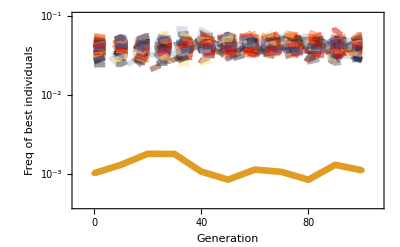

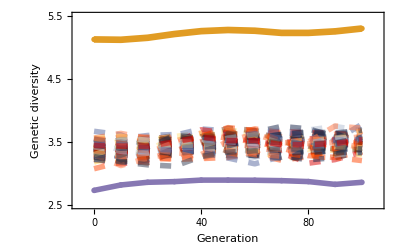

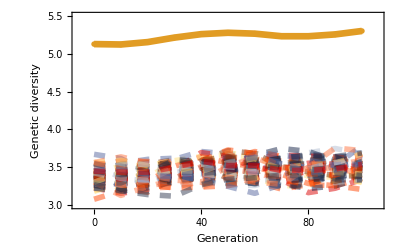

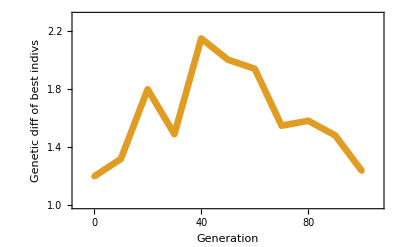

```mathematica
LocalGlobalPlot[maxfitSS,colorSS,maxfitWMC,colorWMC,{{-5,105},{0,0.8}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_" <> nameSSWM,{0.7,0.2}]
LocalGlobalPlot[maxfitSS ,colorSS,"","",{{-6,106},{0,0.8}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_" <> nameSS]
LocalGlobalPlot[maxfitFreqSS,colorSS,maxfitFreqWMC,colorWMC,{{-6,106},{0.0004,0.1}},{"Generation","Freq of best individuals"},{0.5,0.6},{1,"log"},"max_fit_freq_" <> nameSSWM,{0.558,0.45}]
LocalGlobalPlot[maxfitFreqSS,colorSS,"","",{{-6,106},{0.0004,0.1}},{"Generation","Freq of best individuals"},{0.5,0.5},{1,"log"},"max_fit_freq_" <> nameSS]
LocalGlobalPlot[hetSS,colorSS,hetWMC,colorWMC,{{-6,106},{2.5,5.5}},{"Generation","Genetic diversity"},{0.6,0.7},{1,1},"het_" <> nameSSWM,{0.655,0.565}]
LocalGlobalPlot[hetSS,colorSS,"",colorWMC,{{-6,106},{3,5.5}},{"Generation","Genetic diversity"},{0.7,0.6},{1,1},"het_" <> nameSS]
GlobalPlot[relSS,colorSS,{{-6,106},{1,2.3}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSS]
```

#### Supplement

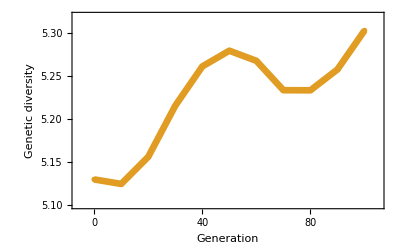

```mathematica
GlobalPlot[hetSS[[-1]],colorSS,{{-6,105},{5.10,5.32}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameSS <> "_global"]
```

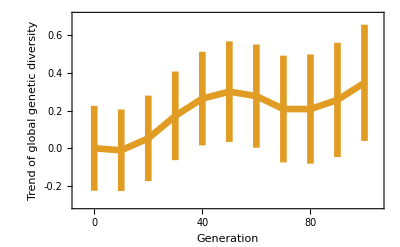

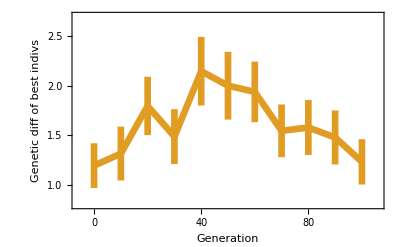

```mathematica
GlobalPlot[hetSS[[-1]],colorSS,{{-6,105},{-0.3,0.7}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameSS <> "_global_sd"]
GlobalPlot[relSS,colorSS,{{-6,106},{0.8,2.7}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSS<>"_sd"]
```

### SB

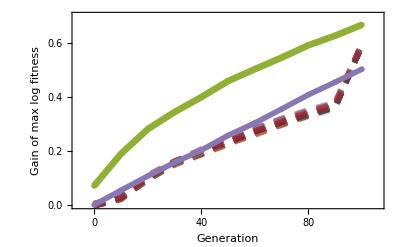

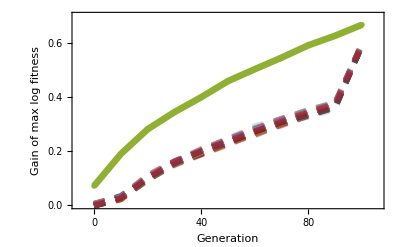

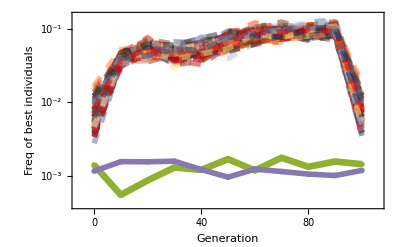

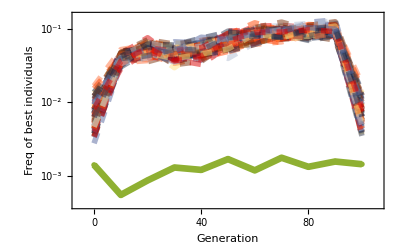

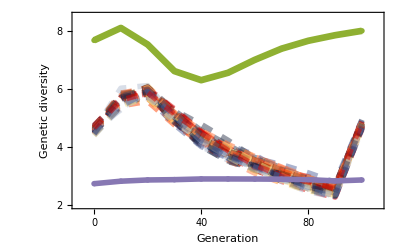

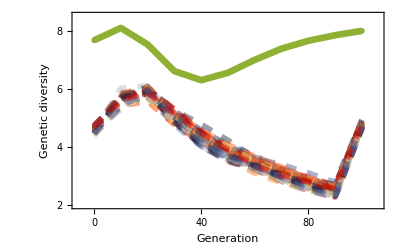

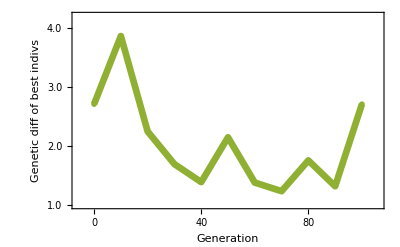

```mathematica
LocalGlobalPlot[maxfitSB,colorSB,maxfitWMC,colorWMC,{{-6,106},{0,0.7}},{"Generation","Gain of max log fitness"},{0.25,0.75},{1,1},"max_fit_" <> nameSBWM,{0.7,0.2}]
LocalGlobalPlot[maxfitSB,colorSB,"","",{{-6,106},{0,0.7}},{"Generation","Gain of max log fitness"},{0.25,0.75},{1,1},"max_fit_" <> nameSB]

LocalGlobalPlot[maxfitFreqSB,colorSB,maxfitFreqWMC,colorWMC,{{-6,106},{0.0004,0.15}},{"Generation","Freq of best individuals"},{0.5,0.6},{1,"log"},"max_fit_freq_" <> nameSBWM,{0.56,0.45}]
LocalGlobalPlot[maxfitFreqSB,colorSB,"","",{{-6,106},{0.0004,0.15}},{"Generation","Freq of best individuals"},{0.5,0.5},{1,"log"},"max_fit_freq_" <> nameSB,""]

LocalGlobalPlot[hetSB,colorSB,hetWMC,colorWMC,{{-6,106},{2,8.5}},{"Generation","Genetic diversity"},{0.695,0.64},{1,1},"het_" <> nameSBWM,{0.745,0.5}]
LocalGlobalPlot[hetSB,colorSB,"","",{{-6,106},{2,8.5}},{"Generation","Genetic diversity"},{0.75,0.6},{1,1},"het_" <> nameSB,""]

GlobalPlot[relSB,colorSB,{{-6,106},{1,4.2}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSB]
```

#### Supplement

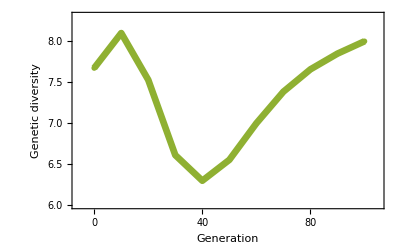

```mathematica
GlobalPlot[hetSB[[-1]],colorSB,{{-6,105},{6.0,8.3}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameSB <> "_global"]
```

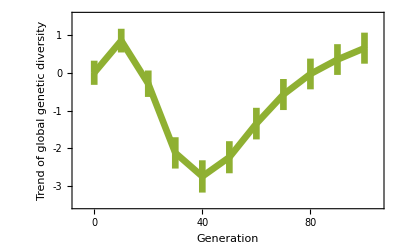

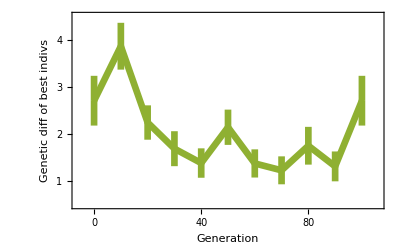

```mathematica
GlobalPlot[hetSB[[-1]],colorSB,{{-6,105},{-3.5,1.5}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameSB <> "_global_sd"]
GlobalPlot[relSB,colorSB,{{-6,106},{0.5,4.5}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSB<>"_sd"]
```

### BS

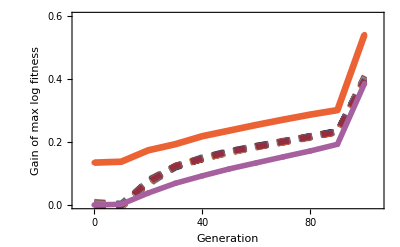

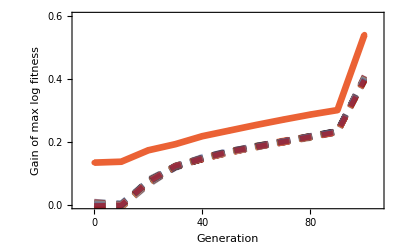

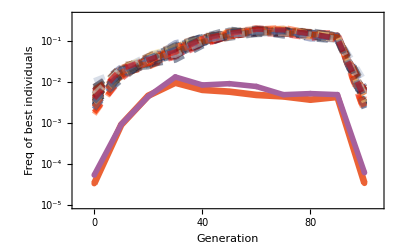

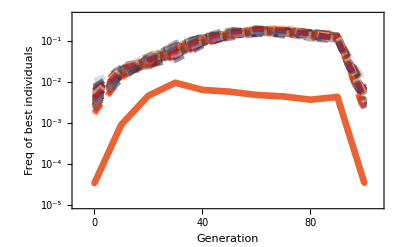

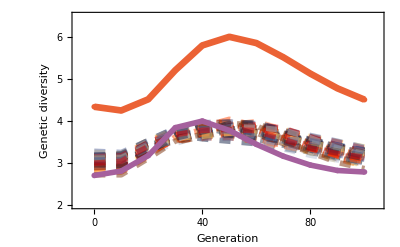

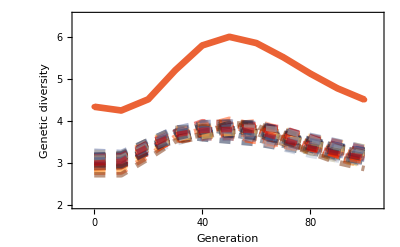

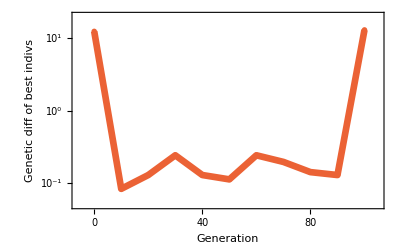

```mathematica
LocalGlobalPlot[maxfitBS,colorBS,maxfitWMB,colorWMB,{{-6,105},{0,0.6}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBSWM,{0.7,0.1}]
LocalGlobalPlot[maxfitBS,colorBS,"","",{{-6,105},{0,0.6}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBS,""]

LocalGlobalPlot[maxfitFreqBS,colorBS,maxfitFreqWMB,colorWMB,{{-6,105},{10^-5,0.4}},{"Generation","Freq of best individuals"},{0.5,0.4},{1,"log"},"max_fit_freq_"<>nameBSWM,{0.56,0.25}]
LocalGlobalPlot[maxfitFreqBS,colorBS,"","",{{-6,105},{10^-5,0.4}},{"Generation","Freq of best individuals"},{0.5,0.3},{1,"log"},"max_fit_freq_"<>nameBS,""]

LocalGlobalPlot[hetBS,colorBS,hetWMB,colorWMB,{{-6,105},{2,6.5}},{"Generation","Genetic diversity"},{0.55,0.65},{1,1},"het_"<>nameBSWM,{0.6,0.13}]
LocalGlobalPlot[hetBS,colorBS,"","",{{-6,105},{2,6.5}},{"Generation","Genetic diversity"},{0.5,0.65},{1,1},"het_"<>nameBS,""]

GlobalPlot[relBS,colorBS,{{-6,105},{0.05,20}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBS]
```

#### Supplement

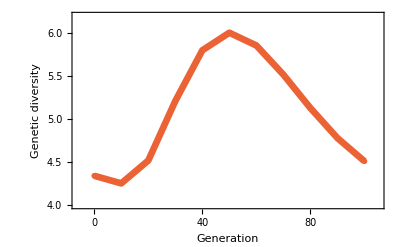

```mathematica
GlobalPlot[hetBS[[-1]],colorBS,{{-6,105},{4.0,6.2}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameBS<> "_global"]
```

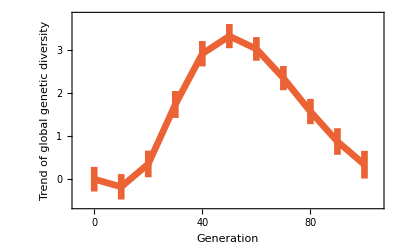

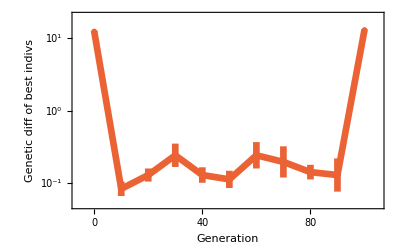

```mathematica
GlobalPlot[hetBS[[-1]],colorBS,{{-6,105},{-0.6,3.8}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameBS<> "_global_sd"]
GlobalPlot[relBS,colorBS,{{-6,105},{5*10^-2,20}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBS<>"_sd"]
```

### BB

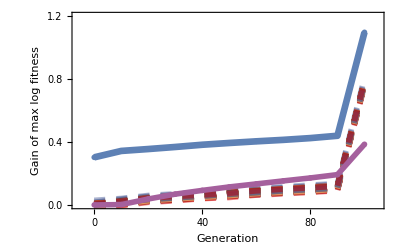

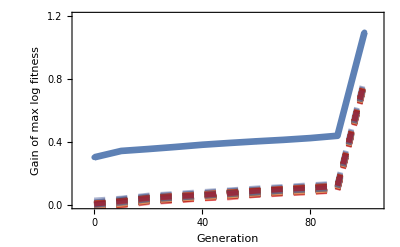

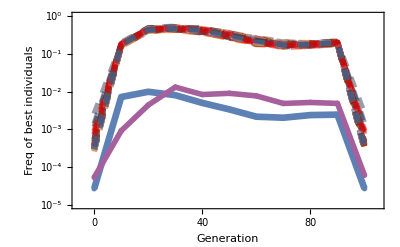

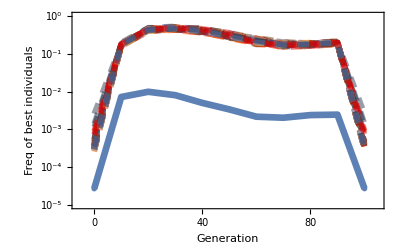

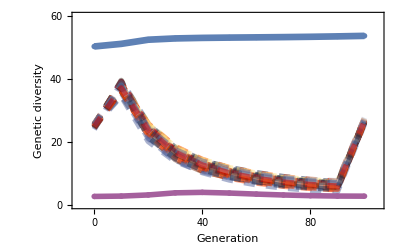

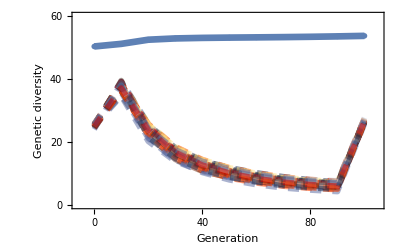

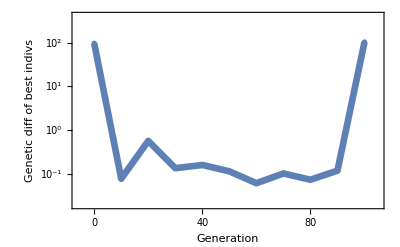

```mathematica
LocalGlobalPlot[maxfitBB,colorBB,maxfitWMB,colorWMB,{{-6,105},{0,1.2}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBBWM,{0.408,0.61}]
LocalGlobalPlot[maxfitBB,colorBB,"","",{{-6,105},{0,1.2}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBB]

LocalGlobalPlot[maxfitFreqBB,colorBB,maxfitFreqWMB,colorWMB,{{-6,105},{10^-5,1}},{"Generation","Freq of best individuals"},{0.4,0.3},{1,"log"},"max_fit_freq_"<>nameBBWM,{0.46,0.14}]
LocalGlobalPlot[maxfitFreqBB,colorBB,"","",{{-6,105},{10^-5,1}},{"Generation","Freq of best individuals"},{0.5,0.2},{1,"log"},"max_fit_freq_"<>nameBB,""]

LocalGlobalPlot[hetBB,colorBB,hetWMB,colorWMB,{{-6,105},{0,60}},{"Generation","Genetic diversity"},{0.6,0.65},{1,1},"het_"<>nameBBWM,{0.655,0.51}]
LocalGlobalPlot[hetBB,colorBB,"","",{{-6,105},{0,60}},{"Generation","Genetic diversity"},{0.6,0.6},{1,1},"het_"<>nameBB,""]

GlobalPlot[relBB,colorBB,{{-6,105},{0.02,400}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBB]
```

#### Supplement

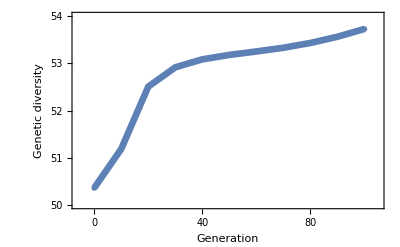

```mathematica
GlobalPlot[hetBB[[-1]],colorBB,{{-6,105},{50,54}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameBB<> "_global"]
```

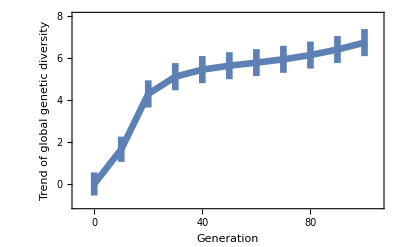

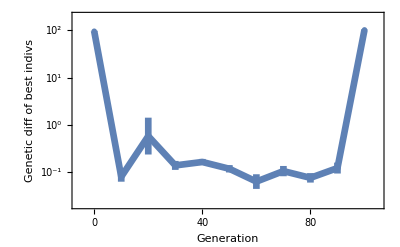

```mathematica
GlobalPlot[hetBB[[-1]],colorBB,{{-6,105},{-1,8}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameBB<> "_global_sd"]
GlobalPlot[relBB,colorBB,{{-6,105},{0.02,200}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBB<>"_sd"]
```

### SSIS

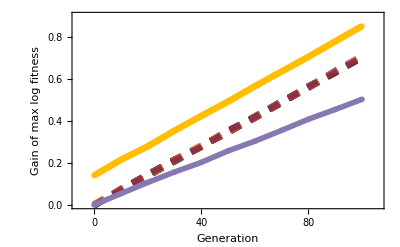

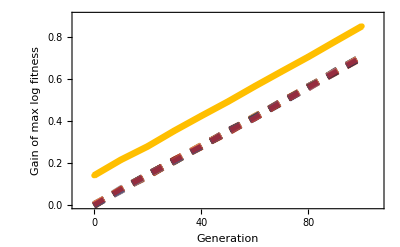

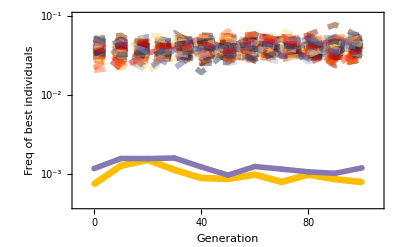

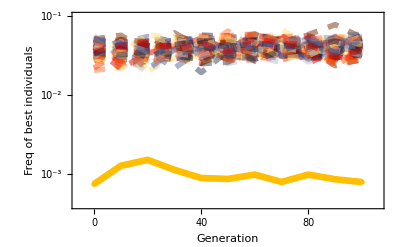

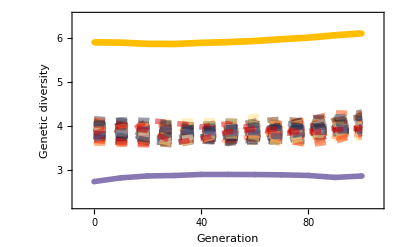

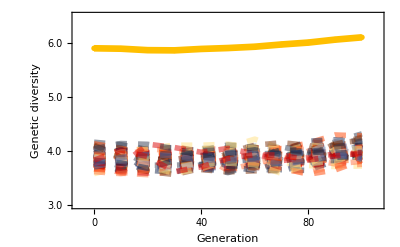

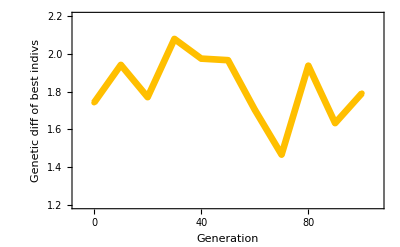

```mathematica
LocalGlobalPlot[maxfitSSIS,colorSSIS,maxfitWMC,colorWMC,{{-6,106},{0,0.9}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_" <> nameSSISWM,{0.7,0.2}]
LocalGlobalPlot[maxfitSSIS,colorSSIS,"","",{{-6,106},{0,0.9}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_" <> nameSSIS]

LocalGlobalPlot[maxfitFreqSSIS,colorSSIS,maxfitFreqWMC,colorWMC,{{-6,106},{0.0004,0.1}},{"Generation","Freq of best individuals"},{0.5,0.6},{1,"log"},"max_fit_freq_" <> nameSSISWM,{0.558,0.45}]
LocalGlobalPlot[maxfitFreqSSIS,colorSSIS,"","",{{-6,106},{0.0004,0.1}},{"Generation","Freq of best individuals"},{0.5,0.5},{1,"log"},"max_fit_freq_" <> nameSSIS]

LocalGlobalPlot[hetSSIS,colorSSIS,hetWMC,colorWMC,{{-6,106},{2.2,6.5}},{"Generation","Genetic diversity"},{0.6,0.7},{1,1},"het_" <> nameSSISWM,{0.655,0.565}]
LocalGlobalPlot[hetSSIS,colorSSIS,"","",{{-6,106},{3,6.5}},{"Generation","Genetic diversity"},{0.7,0.6},{1,1},"het_" <> nameSSIS]

GlobalPlot[relSSIS,colorSSIS,{{-6,106},{1.2,2.2}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSSIS]
```

#### Supplement

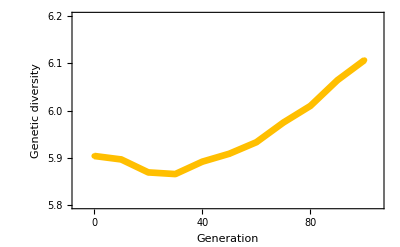

```mathematica
GlobalPlot[hetSSIS[[-1]],colorSSIS,{{-6,105},{5.8,6.2}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameSSIS <> "_global"]
```

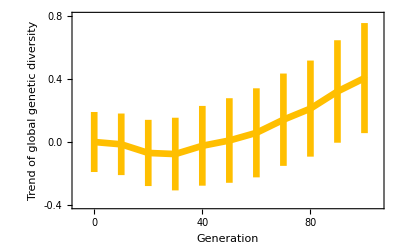

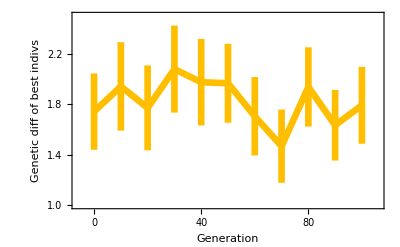

```mathematica
GlobalPlot[hetSSIS[[-1]],colorSSIS,{{-6,105},{-0.4,0.8}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameSSIS <> "_global_sd"]
GlobalPlot[relSSIS,{colorSSIS},{{-6,106},{1,2.5}},{"Generation","Genetic diff of best indivs"},{1,1},"rel_" <> nameSSIS<>"_sd"]
```

### BBIS

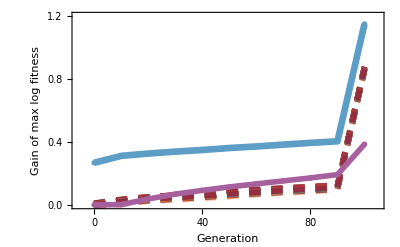

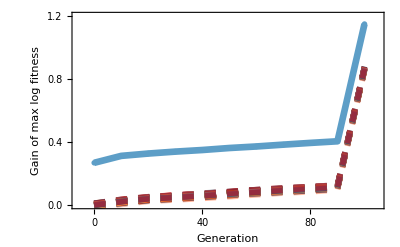

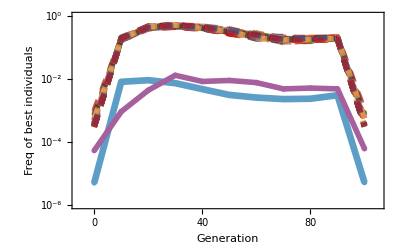

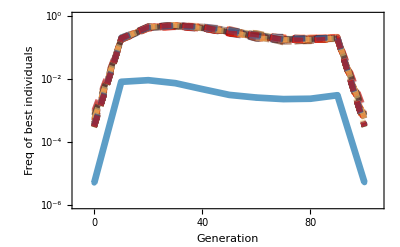

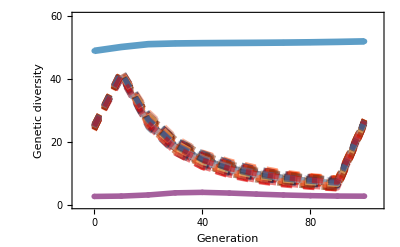

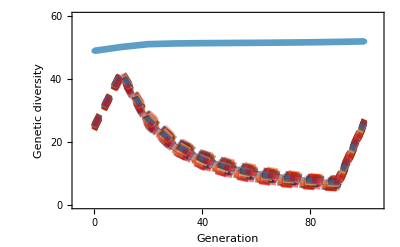

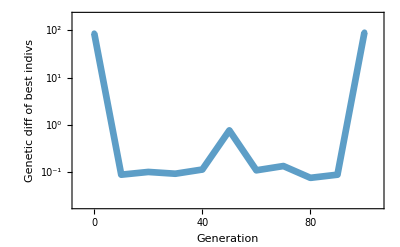

```mathematica
LocalGlobalPlot[maxfitBBIS,colorBBIS,maxfitWMB,colorWMB,{{-6,105},{0,1.2}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBBISWM,{0.408,0.61}]
LocalGlobalPlot[maxfitBBIS,colorBBIS,"","",{{-6,105},{0,1.2}},{"Generation","Gain of max log fitness"},{0.35,0.75},{1,1},"max_fit_"<>nameBBIS]

LocalGlobalPlot[maxfitFreqBBIS,colorBBIS,maxfitFreqWMB,colorWMB,{{-6,105},{10^-6,1}},{"Generation","Freq of best individuals"},{0.4,0.3},{1,"log"},"max_fit_freq_"<>nameBBISWM,{0.46,0.14}]
LocalGlobalPlot[maxfitFreqBBIS,colorBBIS,"","",{{-6,105},{10^-6,1}},{"Generation","Freq of best individuals"},{0.5,0.2},{1,"log"},"max_fit_freq_"<>nameBBIS,""]

LocalGlobalPlot[hetBBIS,colorBBIS,hetWMB,colorWMB,{{-6,105},{0,60}},{"Generation","Genetic diversity"},{0.6,0.65},{1,1},"het_"<>nameBBISWM,{0.655,0.51}]
LocalGlobalPlot[hetBBIS,colorBBIS,"","",{{-6,105},{0,60}},{"Generation","Genetic diversity"},{0.6,0.6},{1,1},"het_"<>nameBBIS]

GlobalPlot[relBBIS,colorBBIS,{{-6,105},{2*10^-2,2*10^2}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBBIS]
```

#### Supplement

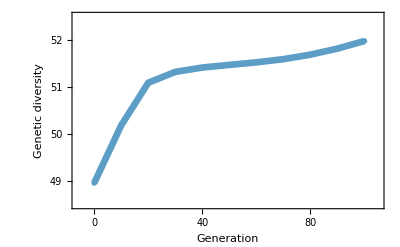

```mathematica
GlobalPlot[hetBBIS[[-1]],colorBBIS,{{-6,105},{48.5,52.5}},{"Generation","Genetic diversity"},{1,1},"het_" <> nameBBIS<> "_global"]
```

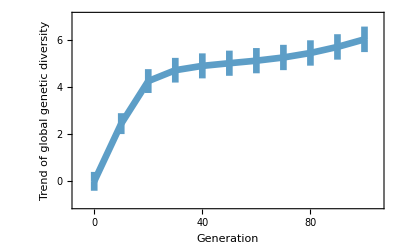

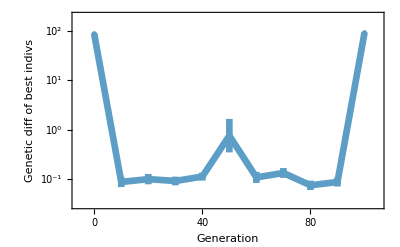

```mathematica
GlobalPlot[hetBBIS[[-1]],colorBBIS,{{-6,105},{-1,7}},{"Generation",Column[{"Trend of global","genetic diversity"},Left,0]},{1,1},"het_" <> nameBBIS<> "_global_sd"]
GlobalPlot[relBBIS,colorBBIS,{{-6,105},{0.03,200}},{"Generation","Genetic diff of best indivs"},{1,"log"},"rel_"<>nameBBIS<>"_sd"]
```

### Relateness - Full

```mathematica
LegendStyle[{"Unsynced","Synced dispersal",},colorList,-1.7]
```

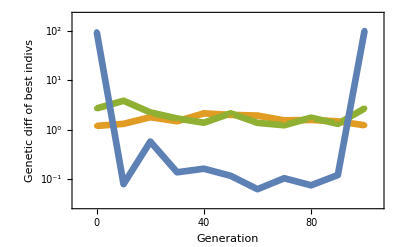

```mathematica
colorList={colorSS,colorSB,colorBB};
GlobalPlot[{relSS,relSB,relBB},colorList,{{-7,105},{3*10^-2,200}},{"Generation","Genetic diff of best indivs"},{1,"log"}]
(*Legended[%,Placed[LegendStyle[{"Unsynced","Synced dispersal",Column[{"Pop synced sex","& dispersal"},Left,0]},colorList,-1.5],{0.5,0.78}]]*)
Export["Plot/rel_SS&SB&BB.pdf",%];
```

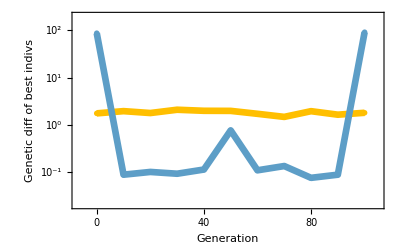

```mathematica
colorList={colorSSIS,colorBBIS};
GlobalPlot[{relSSIS,relBBIS},colorList,{{-7,105},{2*10^-2,200}},{"Generation","Genetic diff of best indivs"},{1,"log"}];
Legended[%,Placed[LegendStyle[{"Indiv synced only","Indiv & pop synced"},colorList],{0.5,0.8}]]
Export["Plot/rel_SSIS&BBIS.pdf",%];
```

## Migrants

```mathematica
tgapList=ToString/@Table[i,{i,0,400,50}];
datab=Importtfit[pathBB<>"Migrant/b/"<>#<>"D100N10000"<>type]&/@tgapList;
speedb=SpeedHA[datab,tgapList];
datar=Importtfit[pathBB<>"Migrant/r/"<>#<>"D100N10000"<>type]&/@tgapList;
speedr=SpeedHA[datar,tgapList];
datam=Importtfit[pathBB<>"Migrant/m/"<>#<>"D100N10000"<>type]&/@tgapList;
speedm=SpeedHA[datam,tgapList];
datar0=Importtfit[pathBB<>"Migrant/r0/"<>#<>"D100N10000M5E-4R0"]&/@tgapList;
speedr0=SpeedHA[datar0,tgapList];
```

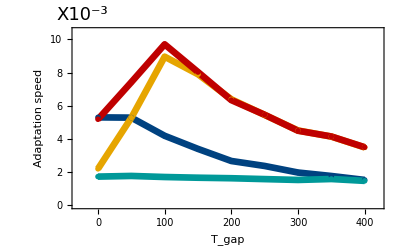

```mathematica
colorList=ColorData[81,"ColorList"];
GlobalPlot[{speedr,speedm,speedb,speedr0},colorList,{{-30,420},{0,0.0105}},{"T_gap","Adaptation speed"},{1,1000}];
Show[%,Epilog->Inset[Style["X10^-3",18],Offset[{-5,-5},Scaled[{0.05,1.1}]]],ImagePadding->{{All,All},{All,30}},PlotRangeClipping->False]/. _Opacity->(##&[]);
Legended[%,Placed[LegendStyle[{"Residents","Migrants","Both","No Rec"},colorList],{0.78,0.78}]]
Export["Plot/Migrants.pdf",%];
```

## Offset

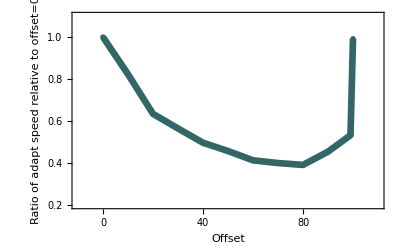

```mathematica
offsetList=Table[i,{i,0,100,10}];offsetList=ToString/@Insert[offsetList,99,-2];
offsettfit=Importtfit[pathBB<>"Interval/100I"<>#<>"D100N10000"<>type]&/@offsetList;
offsetSpeed=SpeedHA[offsettfit,offsetList];offsetRatio=offsetSpeed;
offsetRatio[[;;,2]]=offsetRatio[[;;,2]]/offsetRatio[[1,2]];

GlobalPlot[offsetRatio,ColorData[89,1],{{-10,110},{0.2,1.1}},{"Offset",Column[{"Ratio of adapt speed"," relative to offset=0"},Left,0]},{1,1}]
Export["Plot/Offset.pdf",%];
```

### Statistics

```mathematica
(*Define functions*)
fitpre[fitdata_,dN_,tnew_]:=Module[{fitSplit,fitSplitC,maxfreq,mft,global,globalm,local,localm,stdfit,stdfitm},
fitSplit=SequenceSplit[#,{";"}]&/@fitdata;fitSplitC=Prepend[#,Table[{0,0},dN+1]]&/@Map[SequenceSplit[#,{","}]&,fitSplit[[;;,;;,2;;]],{2}];
maxfreq=Partition[#,Length@tnew,Length@tnew-1]&/@fitSplitC;
mft=Transpose[Transpose[maxfreq,3<->4],4<->5];(*Data Strcuture: runs,times(all tgap),demes,fit/freq,times(1 tgap)*)
global=mft[[;;,;;,-1]];local=mft[[;;,;;,;;-2]];
stdfit=Map[StandardDeviation,local,{2}];stdfitm=Map[Mean,stdfit,{0,1}][[1]];
globalm=Map[Mean,global,{0,1}];localm=Map[Mean,local,{0,2}];
Transpose[{tnew,#}]&/@Flatten[{globalm,localm,{stdfitm}},1](*global fit,global freq,local fit,local freq,var of local fit*)
]
LegendStyleVar[legend_,colorlist_]:=
LineLegend[Directive[colorlist[[#]],Thickness[0.01]]&/@Range[Length[#]],#,LabelStyle->{15},LegendMarkers->None,LegendLayout->{"Row",2},Spacings->{0.3,0.5}]&@legend
path0=NotebookDirectory[];
(*Import data. Takes 6 mins*)
offsetList=Table[i,{i,0,100,10}];offsetList=ToString/@Insert[offsetList,99,-2];
tnewD1=Range[0,100];
offsetFitRaw=Import[pathBB<>"Interval/100I"<>#<>"D100N10000M5E-4R1.25E-3.fit","Table"]&/@offsetList;
datafit=fitpre[#,100,tnewD1]&/@offsetFitRaw;
colorList=Table[ColorData["Rainbow"][i],{i,0,1,1/5}];
(*Select partial data*)
ind = {1,2,4,9,10,11};
offset=offsetList[[#]]&/@ind;offsetFit=datafit[[#]]&/@ind;
offsetFitLocal=Transpose[{#[[;;,1]],#[[;;,2]]-#[[1,2]]}]&/@offsetFit[[;;,3]];(*Shift by localmax*)
(*setting the markers on the right*)
legendH=Partition[offsetFitLocal[[;;,-1]],1];
textStyle=Table[Style[Text[offset[[i]],{100.5,legendH[[i,1,-1]]}],colorList[[i]],12],{i,1,Length@ind}];
textStyle=SortBy[textStyle,#[[1,2,2]]&];
textStyle[[;;,1,2,1]]=Table[If[OddQ[i],101.4,100.8],{i,1,Length@ind}];
```

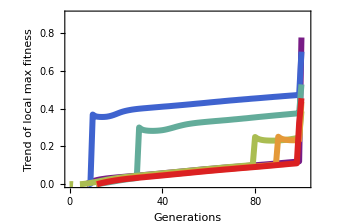

```mathematica
offsetplot=GlobalPlot[offsetFitLocal,colorList,{{0,102},{0,0.9}},{"Generations",Column[{"Trend of","local max fitness"},Left,0]},{1,1},"Offset_LocalMax_no_Legend",None,None];
legendplot=ListPlot[legendH,PlotMarkers->{"-",40},PlotRange->{{95,105},{0,0.9}},Axes->False,PlotStyle->StyleGenerator[colorList,offsetFitLocal],ImageSize->240,Epilog->textStyle];
Export["Plot/Offset_LocalMax_Legend.pdf",%];
Show[offsetplot,ImageSize->Medium,Epilog->{Inset[legendplot,{108,0.46}],Inset[TextCell["offset:",15],{113,0.92}]},ImagePadding->{{All,60},{All,15}},PlotRangeClipping->False]
Export["Plot/Offset_LocalMax.pdf",%];
```

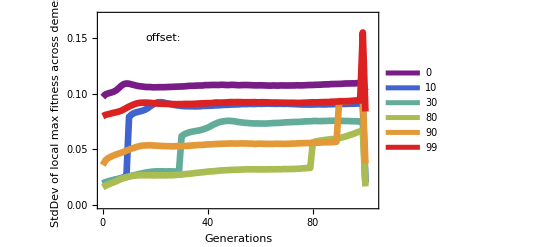

```mathematica
GlobalPlot[offsetFit[[;;,5]],colorList,{{0,103},{0,0.17}},{"Generations",Column[{"StdDev of local max","fitness across demes"},Left,0]},{1,1},"",None,None];
Show[%,Epilog->{Inset[LegendStyleVar[offset,colorList],{60,0.14}],Inset[TextCell["offset:",18],{23,0.15}]}]
Export["Plot/Offset_FitnessStD.pdf",%];
```

#### Full plots

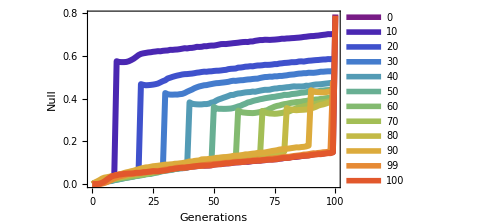

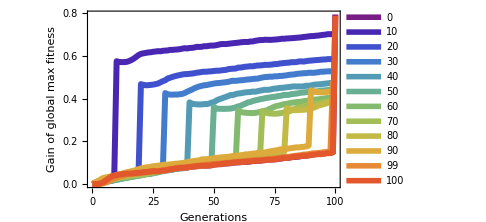

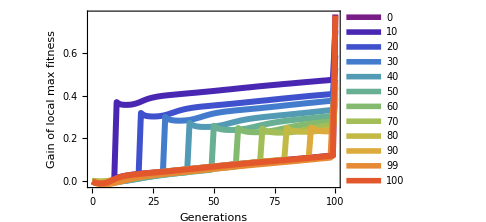

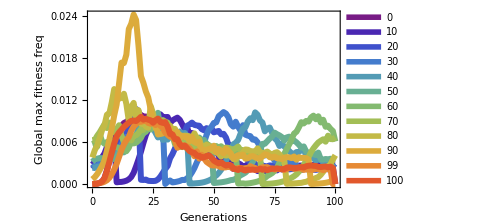

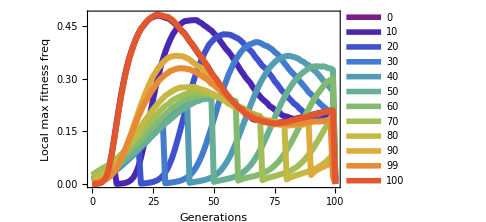

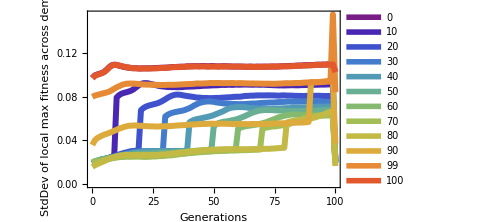

```mathematica
colorList=Table[ColorData["Rainbow"][i],{i,0,1,1/12}];
FullPlot[data_,labels_]:=ListPlot[data,Joined->True,Frame->True,PlotStyle->StyleGenerator[colorList,data],FrameLabel->labels,PlotMarkers->None,PlotLegends->offsetList,PlotRange->All,FrameStyle->Directive[15],ImageSize->Medium]

FullPlot[Transpose[{#[[;;,1]],#[[;;,2]]-#[[1,2]]}]&/@datafit[[;;,1]],{"Generations",}]

FullPlot[Transpose[{#[[;;,1]],#[[;;,2]]-#[[1,2]]}]&/@datafit[[;;,1]],{"Generations","Gain of global max fitness"}]
Export["Plot/Offset_GlobalMax_Full.pdf",%];
FullPlot[Transpose[{#[[;;,1]],#[[;;,2]]-#[[1,2]]}]&/@datafit[[;;,3]],{"Generations","Gain of local max fitness"}]
Export["Plot/Offset_LocalMax_Full.pdf",%];
FullPlot[datafit[[;;,2]],{"Generations","Global max fitness freq"}]
Export["Plot/Offset_GlobalFreq_Full.pdf",%];
FullPlot[datafit[[;;,4]],{"Generations","Local max fitness freq"}]
Export["Plot/Offset_LocalFreq_Full.pdf",%];
FullPlot[datafit[[;;,5]],{"Generations",Column[{"StdDev of local max","fitness across demes"},Left,0]}]
Export["Plot/Offset_FitnessVar_Full.pdf",%];
```

## Supplementary

### w/ and w/o sex

```mathematica
StyleGenerator[colorlist_,data_]:=Module[{len,colorlistN},
colorlistN=If[Head[colorlist]===List,colorlist,{colorlist}];
len=If[Length@Dimensions[data]==2,1,Dimensions[data][[1]]];
Table[{colorlistN[[i]],Thickness[0.008]},{i,1,len}]
]
```

```mathematica
R0Type={"100D10N100000M5E-4R0","100D100N10000M5E-4R0"};
{SpeedSS10R0,SpeedSS100R0}=SpeedHA[{Importtfit[pathSS<>#]},{10^6},True]&/@R0Type;
{SpeedSB10R0,SpeedSB100R0}=SpeedHA[{Importtfit[pathSB<>#]},{10^6},True]&/@R0Type;
speed={{SpeedWMCR0,SpeedSS10R0,SpeedSS100R0,SpeedSB10R0,SpeedSB100R0},{SpeedWMC,SpeedSS10,SpeedSS100,SpeedSB10,SpeedSB100}}[[;;,;;,-1,2]];speed=Map[{Flatten@#}&,Transpose[speed]];
```

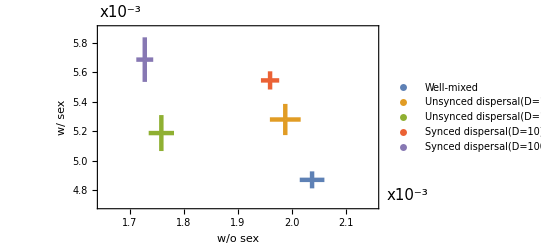

```mathematica
GlobalPlot[speed,ColorData[97,"ColorList"],{{1.65*10^-3,2.15*10^-3},{4.7*10^-3,5.89*10^-3}},{"w/o sex", "w/ sex"},{1000,1000},"",None,None];
Show[%,Epilog->{Inset[Style[Row[{"x",ScienForm[0.001]}],15],Offset[{-5,-5},Scaled[{0.1,1.1}]]],Inset[Style[Row[{"x",ScienForm[0.001]}],15],Offset[{-5,-5},Scaled[{1.12,0.1}]]]},ImagePadding->{{All,45},{All,25}},PlotRangeClipping->False];
Legended[%,Placed[PointLegend[97,{"Well-mixed","Unsynced dispersal(D=10)","Unsynced dispersal(D=100)","Synced dispersal(D=10)","Synced dispersal(D=100)"},LabelStyle->{15},LegendMarkerSize->20,Spacings->{0.5,0.1}],Right]]
Export["Plot/SpeedCompare.pdf",%];
```